0.477465

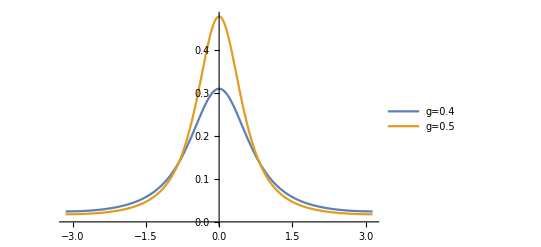

```mathematica
HenyeyGreenstein[t_, g_]:= 1 / (4 * Pi) * (1 - g^2) / ((1 + g^2 - 2 * g * Cos[t])^(3/2));
HenyeyGreenstein[0, 0.5]
functions=Table[HenyeyGreenstein[x, g], {g, Range[0.4, 0.5, 0.1]}];
legends = Table[StringForm["g=``", x], {x, Range[0.4, 0.5, 0.1]}];
Plot[functions, {x, -Pi, Pi}, PlotLegends->legends, PlotRange->Automatic]
```

```mathematica
Integrate[1 / (4 * Pi) * (1 - g^2) / ((1 + g^2 - 2 * g * Cos[x])^(3/2)), {x, -Pi, Pi}]
```

ConditionalExpression[-(√((1+g)^2) EllipticE[(4 g)/(1+g)^2])/((-1+g^2) π), ]

```mathematica
Integrate[1 / (4 * Pi) * (1 - 0.25) / ((1 +0.25 - Cos[x])^(3/2)), {x, -Pi, Pi}]
```

0.70903-6.39494×10^-16 ⅈ

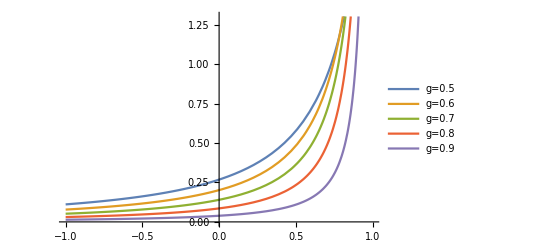

```mathematica
HenyeyGreensteinCos[t_, g_]:= 0.5 * (1 - g^2) / ((1 + g^2 - 2 * g * t)^(3/2));
functions=Table[HenyeyGreensteinCos[x, g], {g, Range[0.5, 0.9, 0.1]}];
legends = Table[StringForm["g=``", x], {x, Range[0.5, 0.9, 0.1]}];
Plot[functions, {x, -1, 1}, PlotLegends->legends, PlotRange->Automatic]
```

```mathematica
Integrate[0.5 * (1 - g^2) / ((1 + g^2 - 2 * g * x)^(3/2)), {x, -1, 1}]
```

ConditionalExpression[((0.5-0.5 g^2) (1/(√(1.+(-2.+g) g))-1./(√(1.+g (2.+g)))))/g, ]

```mathematica
Integrate[0.5 * (1 - g^2) / ((1 + g^2 - 2 * g * x)^(3/2)), {x, -1, x}]
```

ConditionalExpression[-(1. (0.5-0.5 g^2))/(g √(1.+2. g+g^2))+(0.5-0.5 g^2)/(g √(1.+g^2-2. g x)), ]

```mathematica
result=FullSimplify[D[-(1.(0.5-0.5* g^2))/(g √(1.+2.* g+g^2))+(0.5-0.5 * g^2)/(g √(1.+g^2-2.* g * x)), x]]
```

(0.5-0.5 g^2)/((1.+g^2-2. g x)^(3/2))

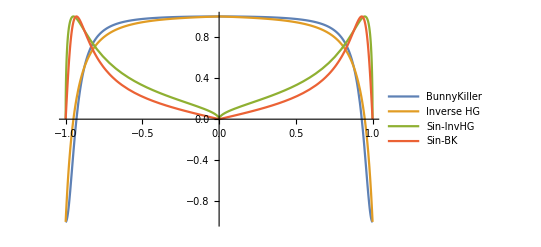

```mathematica
BunnyKiller[t_, g_] := Cos[2 * ArcTan[(1 - g) / (1 + g) * Tan[Pi / 2 * t]]];
InvHG[t_, g_] := (1 + g^2 - ((1 - g^2)/ (1 - g + 2 * g * (-Abs[t]+1.0)))^2) / 2 / g;
func2plot = List[BunnyKiller[x, 0.8],  InvHG[x, 0.8], Sqrt[1 - InvHG[x, 0.8]^2],  Sqrt[1 - BunnyKiller[x, 0.8]^2]];
legends = List["BunnyKiller", "Inverse HG", "Sin-InvHG", "Sin-BK"];
Plot[func2plot, {x, -1 + 0.000001, 1 - 0.000001}, PlotLegends->legends, PlotRange->Automatic]
```

```mathematica
Integrate[(1 + Cos[x]^2)* Sin[x], {x, 0, Pi}]
```

8/3

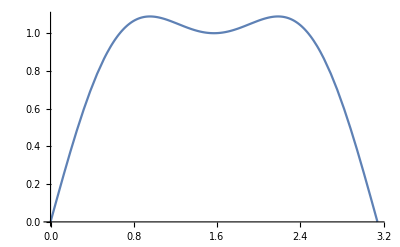

```mathematica
Plot[(1 + Cos[x]^2) * Sin[x], {x, 0, Pi}]
```